Represent a graph as a list of it nodes, each node a list {m_i,{n_j1,n_j2,n_jN},ϕ_i}; with m_j∈ℕ^+ an integer (the amount of marbles at node m); {n_j1,n_j2,n_jN} the list of neighbors of node m; and ϕ_j the phase that determines if marbles are able to leave the node or not. When Sin[ω t+ϕ_i]≥ 0 marbles can leave the node.
Given a network, the rules of the simulation are that at every tick:
	■ Every node passes one of its marbles to one of its neighbors. The marble is passed if Sin[ω t+ϕ_i]≥ 0, otherwise the marble stays. The marble goes to one of the node’s neighbor with equal probability.

graphToNet[graph, fun] takes a graph (Mathematica style) and returns a list {{m_1,{n_11,n_12,n_(1 N_1)},ϕ_1},…,{m_i,{n_(j 1),n_(j 2),n_(j N_j)},ϕ_j},…,{m_N,{n_(N 1),n_(N 2),n_(N N_N)},ϕ_N}}; with N the number of nodes in the graph, n_(j s) the s-th neighbour of node j, m_j∈[1,N] an integer, and ϕ_j determined by fun.

```mathematica
graphToNet[g_Graph,ϕ_:(RandomChoice[{0,π/2}]&)]:=Module[{nei=Flatten[Position[#,1]]&/@Normal[AdjacencyMatrix[g]],n=VertexCount[g]},
{RandomInteger[n],#,ϕ[]}&/@nei
]
```

netEvolve[graph, ω,T] takes a graph (represented as previously described), with N nodes, an integer T, and a real ω and implements the rule described above for T ticks. It returns an M×T matrix where every row has the number of marbles  of its corresponding node for each tick. This is, element e_(m,t) is the number of marbles of node m at tick t.

netEvolveTrace[graph, ω,T] does the same as netEvolve, but it returns a list {{{s_11,…,s_N1},…,{s_(1T),…,s_(N T)}}},E} with s_(n t) the number of the node that received the marble from node n at time t.

```mathematica
ω=1/2;
```

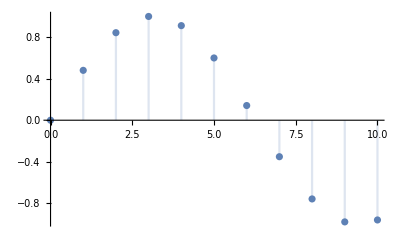

```mathematica
DiscretePlot[Sin[ω t], {t,0,10}]
```

```mathematica
netEvolve[graph_List,ω_Real?Positive,T_Integer]:=Module[
{output=graph[[All,1]],nodes=Length[graph],add,remove,t,tmp},
remove[node:{0,neighs_,ϕ_}]:=node;
remove[node:{m_,neighs_,ϕ_}]:=If[Sin[ω t+ϕ]<0,node,{{m-1,neighs,ϕ},RandomChoice[neighs]}];
t=0;
add=remove/@graph (*remove marble at each node, note where it goes*);
tmp=Cases[add,{_List,i_}->i](*get the destination nodes*);
add=add/.{node_List,i_Integer}->node(*clean the network*);
tmp={#,Count[tmp,#]}&/@Union[tmp](*count how many marbles go to each node*);
tmp=({#[[1]],1}->add[[#[[1]],1]]+#[[2]])&/@%tmp(*build rules to add marbles*);
AppendTo[output,ReplacePart[add,tmp]](*add marbles*);
For[t=1,t≤T,t++,
(*Print[{remove[graph[[1]]],Sin[ω t+graph[[1,3]]]}]*)
add=remove/@graph[[-1]] (*remove marble at each node, note where it goes*);
tmp=Cases[add,{_List,i_}->i](*get the destination nodes*);
add=add/.{node_List,i_Integer}->node(*clean the network*);
tmp={#,Count[tmp,#]}&/@Union[tmp](*count how many marbles go to each node*);
tmp=({#[[1]],1}->add[[#[[1]],1]]+#[[2]])&/@%tmp(*build rules to add marbles*);
AppendTo[output,ReplacePart[add,tmp]](*add marbles*);
];
output
]
```

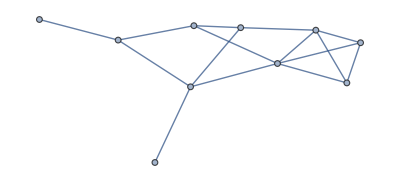

```mathematica
gr=RandomGraph[{10,15}]
```

```mathematica
test=graphToNet[gr]
```

{{7,{4,8,10},0},{6,{5},π/2},{10,{7},π/2},{1,{1,5,8,9,10},π/2},{8,{2,4,6,7},0},{4,{5,8,9},0},{10,{3,5,9},0},{8,{1,4,6,10},0},{2,{4,6,7},π/2},{4,{1,4,8},0}}

```mathematica
ω=12;t=0;
```

```mathematica
remove[node:{0,neighs_,ϕ_}]:=node;
remove[node:{m_,neighs_,ϕ_}]:=If[Sin[ω t+ϕ]<0,node,{{m-1,neighs,ϕ},RandomChoice[neighs]}];
```

```mathematica
remove/@test
```

{{{6,{2,5,6,7,10},0},7},{{8,{1,3,5,6,9,10},0},6},{0,{2},π/2},{0,{6},0},{{1,{1,2,7,9},0},2},{{7,{1,2,4,7,8},0},8},{{1,{1,5,6},0},6},{0,{6},0},{{5,{2,5},π/2},2},{{2,{1,2},0},1}}

```mathematica
Cases[%6,{_List,i_}->i]
```

{7,6,2,8,6,2,1}

```mathematica
%6/.{node_List,i_Integer}->node
```

{{6,{2,5,6,7,10},0},{8,{1,3,5,6,9,10},0},{0,{2},π/2},{0,{6},0},{1,{1,2,7,9},0},{7,{1,2,4,7,8},0},{1,{1,5,6},0},{0,{6},0},{5,{2,5},π/2},{2,{1,2},0}}

```mathematica
{#,Count[%11,#]}&/@Union[%11]
```

{{1,1},{2,2},{6,2},{7,1},{8,1}}

```mathematica
({#[[1]],1}->%12[[#[[1]],1]]+#[[2]])&/@%19
```

{{1,1}→7,{2,1}→10,{6,1}→9,{7,1}→2,{8,1}→1}

```mathematica
ReplacePart[%12,%21]
```

{{7,{2,5,6,7,10},0},{10,{1,3,5,6,9,10},0},{0,{2},π/2},{0,{6},0},{1,{1,2,7,9},0},{9,{1,2,4,7,8},0},{2,{1,5,6},0},{1,{6},0},{5,{2,5},π/2},{2,{1,2},0}}